#### Symmetric real random matrix

```mathematica
directory=SetDirectory[NotebookDirectory[]]
Needs["PacletManager`"]
PacletInstall[directory<>"/MaTeX-1.7.8.paclet"]
<<MaTeX`
```

```mathematica
(* size of the random matrix *)
```

```mathematica
n=5000;
(* mean and standard deviation *)
J=1;
σ=J/(√n);
m=M0/n;
M0=0;
(* list of energies *)
energies={};
```

```mathematica
(* number of samples *)
```

```mathematica
samples=1;
For[ns=1,ns<=samples,ns++,
(* Generate symmetric real random matrix H *)
Hij=Table[If[i<=j,RandomVariate[NormalDistribution[m,σ],1][[1]],0],{i,1,n},{j,1,n}];
H=(Hij+Transpose[Hij]);
(* Find and sort energy levels *)
energies=Join[energies,Sort[ Eigenvalues[H]]]];
```

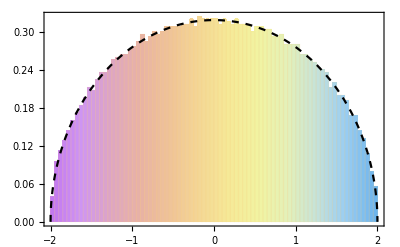

```mathematica
Show[Histogram[energies,80,"PDF",ChartStyle->"Pastel",Frame->True,AspectRatio->1/GoldenRatio,FrameStyle->Directive[Black,12],FrameLabel->{{MaTeX["\\rho(\lambda)",Magnification->1.5],None},{MaTeX["\\text{$\lambda$}",Magnification->1.5],MaTeX["\\text{$N=5000$, $J = 1$, $M_{0}=0$}",Magnification->1.3]}}],Plot[1/(2π J^2)√(4 J^2-λ^2),{λ,-2J,2J},PlotStyle->{Black,Dashed}]]
```